## DIG/CSC 120: Programming in the Humanities Davidson College Dr. Jakub Kabala

Kate, good work here. Watch out for some costly redundancy in your code in #1 and #3, though. TextWords[...], and therefore Flatten[...], are redundant, and not necessary-- they also make your code run a very long time. Take some more care with styling also, both your plots in #3 and #4 and your answer in #5 (use Text). 
B+

## Quiz 4

### Guidelines:

You must work alone.

You have 120 min to complete the quiz. Time begins once you open the Quiz notebook.

This is an open-book quiz: you may consult the Help files in Mathematica, course notes, etc.

Due by Friday, Feb 26th, 5:00 PM in the Moodle Assignment drop.

Fill out the Honor Pledge below

### Honor Pledge (must be signed before you submit):

“I pledge that in completing the problems below I have followed the instructions above and adhered to the standards of the Davidson Honor Code.”

Time & date begun: 1:00
Time & date ended: 2:25
Total time spent: 
Your name: Kate Gilman

### Problems

Count the number of words in WordList[...] that end with “z”.

```mathematica
Count[StringTake[StringReverse[Flatten[TextWords[WordList[]]]],1],"z"]
```

32

Count the number of “z”s that occur anywhere in all the words in WordList[...]

```mathematica
Total[StringCount[WordList[],"z"]]
```

1057

Create a bar chart showing the number of times each letter of the alphabet appears as the final letter of a word in WordList[...]. Include options for a title, axes labels, and chart labels. Your result should look something like this (don’t worry about italicizing the labels):

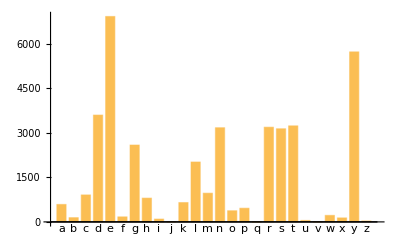
-Graphics-Letter

```mathematica
BarChart[Table[Count[StringTake[StringReverse[Flatten[TextWords[WordList[]]]],1],x],{x,Alphabet[]}],ChartLabels-> {Alphabet[]},PlotLabel-> "Word Ending Letters" ]
```

Here is a string of the Gettysburg Address:

```mathematica
gettysburg=ExampleData[{"Text","GettysburgAddress"}];
```

Make a bar chart showing the length (in words) of each sentence in the Gettysburg Address. Use appropriate options to give your output a plot label, axes labels, and chart labels.  For example:

-Graphics-

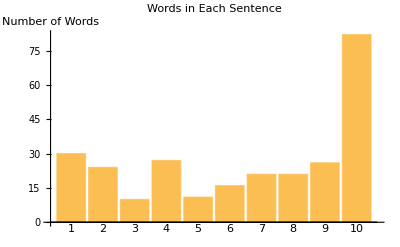

```mathematica
BarChart[WordCount[TextSentences[gettysburg]],ChartLabels-> Range[10],PlotLabel-> "Words in Each Sentence",LabelStyle->Directive[Bold],AxesLabel->"Number of Words",AxesLabel->"Sentence"]
```

Write a couple sentences of interpretation about #4. What do the results reveal about Lincoln’s rhetorical strategy?

```mathematica
From the Bar chart we can see that the last sentence has many more words than all of the other sentences prior. This shows that Lincoln clearly left the audience with a long lasting thought, which he described in his long final sentence.
```